```mathematica
(*The rate matrix Λ is the sum of a diagonal and an off-diagonal matrix. n is the size of depth of the tree, k is the level we want to condition out. Recall each kT_k is exponential with parameter (k-2)/2. *)
makeDiagList[k_,n_] := Table[If[i!=k, -(i-1)/2, Nothing],{i,n,2,-1}]
```

```mathematica
makeOffDiagList[k_,n_]:=  Switch[Boole[k-2 == 0], 1, Table[If[i!=k,(i-1)/2, Nothing], {i,n,4,-1}], 0,  Table[If[i!=k, (i-1)/2,Nothing],{i,n,3,-1}]]
```

```mathematica
Λ[k_,n_]:=DiagonalMatrix[makeDiagList[k,n]]+DiagonalMatrix[makeOffDiagList[k,n],1]
```

```mathematica
Λ[2,5]//MatrixForm
```

(-2 | 2 | 0
0 | -3/2 | 3/2
0 | 0 | -1)

```mathematica
Λ[4,10]//MatrixForm
```

(-9/2 | 9/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | -4 | 4 | 0 | 0 | 0 | 0 | 0
0 | 0 | -7/2 | 7/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | -3 | 3 | 0 | 0 | 0
0 | 0 | 0 | 0 | -5/2 | 5/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | -2 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2)

```mathematica
(*Integrating to obtain the probability that a given mutation occurred on level k*)
```

```mathematica
F[u_,k_,n_]:=Integrate[MatrixExp[t*Λ[k,n]]/(t+u), {t, 0, Infinity}, Assumptions->Element[u,Reals] && u >= 0]
```

```mathematica
f[u_,k_,n_]:= -Table[If[i==1, 1, 0],{i,n-2}].Λ[k,n].F[u,k,n].Table[1,{i,n-2}]
```

```mathematica
P[k_,n_]:= (k-1)/2*Integrate[u*f[u,k,n]*Exp[-(k-1)*u/2],{u,0,Infinity}]
```

```mathematica
N[P[2,5]]
```

0.425515

```mathematica
probs5 = Table[P[i,5]//FullSimplify,{i,2,5}]
```

{4-(44 Log[2])/3+Log[729],2 (-3+Log[729/32]),4-6 Log[3]+Log[16],-1+2 Log[(1024 2^(1/3))/729]}

```mathematica
N[probs]
```

{0.425515,0.251876,0.180915,0.141694}

```mathematica
Total[probs]//FullSimplify
```

1

```mathematica
ListPlot[{probs5,IndepProbs5}, DataRange->{2,5}, PlotRange->{{1,6},Automatic},
PlotLegends->{"true probability", "independence approximation"}, AxesLabel->{Style[k,Bold], Style["P(K=k)",Bold]}, PlotLabel->"n = 5"]
```

-Graphics-

```mathematica
Show[%62,ImageSize->Large]
```

Show::gtype: Out is not a type of graphics.

Show[%62,ImageSize→Large]

```mathematica
Export["/home/farid/Documents/Wolfram Mathematica/n5.png",%63,"PNG"]
```

/home/farid/Documents/Wolfram Mathematica/n5.png

```mathematica
Show[%27,Axes->True,AxesStyle->Black]
```

Show::gtype: Out is not a type of graphics.

Show[%27,Axes→True,AxesStyle→GrayLevel[0]]

```mathematica
Const10= Sum[2/(i-1),{i,2,10}]
```

7129/1260

```mathematica
Const5 = Sum[2/(i-1), {i,2,5}]
```

25/6

```mathematica
(*Probability of K=i under the independece approximation*)
```

```mathematica
IndepProbs10 = Table[2/(i-1)*1/Const, {i,2,10}]
```

{2520/7129,1260/7129,840/7129,630/7129,504/7129,420/7129,360/7129,315/7129,280/7129}

```mathematica
IndepProbs5 = Table[2/(i-1)*1/Const5, {i,2,5}]
```

{12/25,6/25,4/25,3/25}

```mathematica
Err = probs5/IndepProbs5
```

{25/12 (4-(44 Log[2])/3+Log[729]),25/3 (-3+Log[729/32]),25/4 (4-6 Log[3]+Log[16]),25/3 (-1+2 Log[(1024 2^(1/3))/729])}

```mathematica
N[Err]
```

{0.88649,1.04948,1.13072,1.18079}

```mathematica
(*Errors of up to ~20%*)
```

```mathematica
(*Now we will make n larger. Intuitively, this should make the independence approximation more realistic.*)

Clear[probs]
```

```mathematica
probs[n_]:=Table[N[P[i,n]],{i,2,n}]
```

```mathematica
probs[10]
```

$Aborted

```mathematica
probs = Out[213]
```

{0.309778,0.175883,0.123591,0.0954483,0.0778066,0.0656946,0.0568579,0.0501231,0.0448186}

```mathematica
Err = probs/IndepProbs
```

{0.876351,0.995134,1.0489,1.08008,1.10056,1.11509,1.12594,1.13437,1.14111}

```mathematica
(*Still not a wonderful approximation, but maybe workable depending on the context. Also, the approximation works much better for intermediate values of K. Moving to the extremes it K=2 and K=n breakes it down. I somehow expect that this will always be the case *)
```

```mathematica
probs5 = probs
```

probs

```mathematica
IndepProbs5 = IndepProbs
```

{12/25,6/25,4/25,3/25}

```mathematica
probs10 = {0.3097777521693956,0.1758827631645285,0.12359054576455719,0.09544825143092339,0.07780655440188866,0.06569458508340631,0.056857869534906055,0.0501231102877,0.04481856816298091}
```

{0.309778,0.175883,0.123591,0.0954483,0.0778066,0.0656946,0.0568579,0.0501231,0.0448186}

```mathematica
IndepProbs10 = IndepProbs
```

{2520/7129,1260/7129,840/7129,630/7129,504/7129,420/7129,360/7129,315/7129,280/7129}

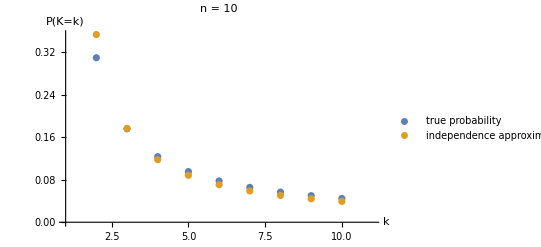

```mathematica
ListPlot[{probs10,IndepProbs10}, DataRange->{2,10}, PlotRange->{{1,11},Automatic},
PlotLegends->{"true probability", "independence approximation"}, AxesLabel->{Style[k,Bold], Style["P(K=k)",Bold]},PlotLabel->"n = 10"]
```

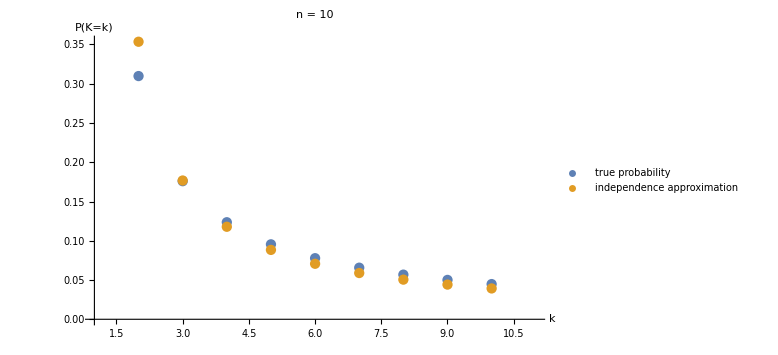

```mathematica
Show[%52,ImageSize->Large]
```

```mathematica
Export["/home/farid/Documents/Wolfram Mathematica/n10.png",%53,"PNG"]
```

/home/farid/Documents/Wolfram Mathematica/n10.png

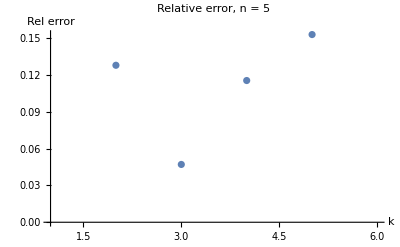

```mathematica
ListPlot[Abs[probs5-IndepProbs5]/probs5, DataRange->{2,5}, PlotRange->{{1,6},Automatic}, AxesLabel->{Style[k,Bold],"Rel error"},PlotLabel->"Relative error, n = 5"]
```

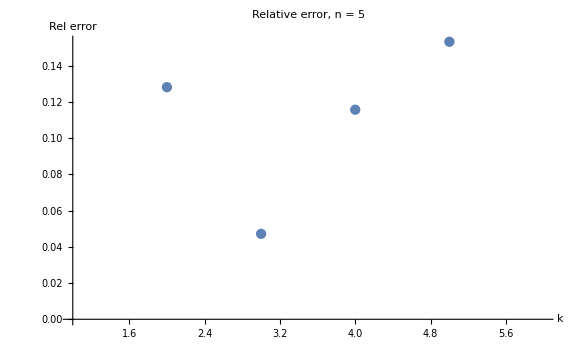

```mathematica
Show[%65,ImageSize->Large]
```

```mathematica
Export["/home/farid/Documents/Wolfram Mathematica/RelErrorN5.png",%66,"PNG"]
```

/home/farid/Documents/Wolfram Mathematica/RelErrorN5.png

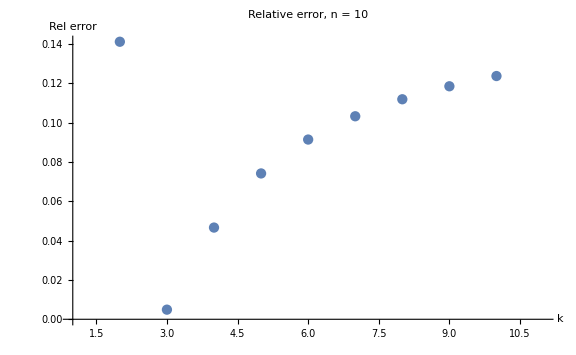

```mathematica
Show[%56,ImageSize->Large]
```

```mathematica
Export["/home/farid/Documents/Wolfram Mathematica/RelErrorn10.png",%57,"PNG"]
```

/home/farid/Documents/Wolfram Mathematica/RelErrorn10.png